## Initialization

### Earth

```mathematica
earth=Entity["Planet","Earth"]
```

Earth

```mathematica
raE=UnitConvert[earth["Apoapsis"],"AstronomicalUnit"];
rpE=UnitConvert[earth["Periapsis"],"AstronomicalUnit"];
aE=earth["MajorAxis"]/2;
bE=earth["MinorAxis"]/2;

iE=earth["Inclination"];
longAscNE=earth["AscendingNodeLongitude"];
argPerE=earth["PeriapsisArgument"];

nE=UnitConvert[earth["MeanMotion"],"Radians"/"JulianYears"];
periodE=UnitConvert[earth["OrbitPeriod"],"JulianYears"];

lastApoapsisE=earth["ApoapsisTimeLast"];

axialtiltE=Quantity[23.44,"Degrees"];
```

### Halley’s Comet

```mathematica
halley=Entity["Comet","Comet1PHalley"]
```

1P/Halley

```mathematica
(* https://en.wikipedia.org/wiki/Orbital_elements *)
raH=UnitConvert[halley["Apoapsis"],"AstronomicalUnit"];
rpH=UnitConvert[halley["Periapsis"],"AstronomicalUnit"];
aH=halley["MajorAxis"]/2;
bH=halley["MinorAxis"]/2;

iH=halley["Inclination"];
longAscNH=halley["AscendingNodeLongitude"];
argPerH=halley["PeriapsisArgument"];

nH=UnitConvert[halley["MeanMotion"],"Radians"/"JulianYears"];
periodH=halley["OrbitPeriod"];

lastApoapsisH=halley["ApoapsisTimeLast"];
```

## Solution 1 (Data Approach): Astronomical Computation Built-ins

Sets the `time` and `dist` variables to the solutions found.

```mathematica
itv={0,QuantityMagnitude[periodE*periodH]}+N[DateValue["Year"]];

newtime=NMinimize[
{
QuantityMagnitude[AstroDistance[halley,Dated[earth,x]]],
Between[x,itv]
},
{x}
];

dist=Quantity[%[[1]],"AstronomicalUnit"]
time=Quantity[%%[[2,1,2]]-DateValue[lastApoapsisE,"Year"],"JulianYears"]
```

AstroDistance::date: Expression Earth cannot be interpreted as a date specification.

General::stop: Further output of AstroDistance::date will be suppressed during this calculation.

0.344372 au

37.8732 a

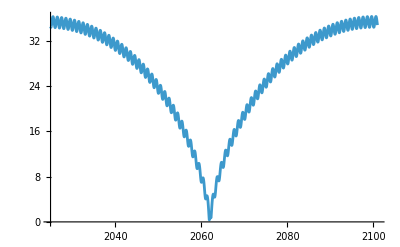

```mathematica
Plot[AstroDistance[halley,Dated[earth,x]],Prepend[itv,x]]
```

## Solution 2 (Mathematical & Visual Approach): Uniform Parametrization of Orbits

Sets the `time` and `dist` variables to the solutions found.

### Parametric Orbit for Earth

```mathematica
apoapsisOffs=2*Pi*QuantityMagnitude[lastApoapsisH-lastApoapsisE,"JulianYears"]/QuantityMagnitude[periodE]
```

-2.7867442

```mathematica
centerE={QuantityMagnitude[aE-rpE],0,0};
posE[t_]=centerE+{
QuantityMagnitude[aE]*Cos[t+apoapsisOffs],
QuantityMagnitude[bE]*Sin[t+apoapsisOffs],
0
};
%//MatrixForm
Show[
ParametricPlot3D[posE[t],{t,0,2*Pi}],
Graphics3D[{
Yellow,Ball[{0,0,0},0.2],
Red,Ball[posE[0],0.05]
}]
]
```

(0.0167102+1.0000001 Cos[2.7867442-t]
-0.99986048 Sin[2.7867442-t]
0)

-Graphics3D-

```mathematica
emE=EulerMatrix[
{
QuantityMagnitude[UnitConvert[iE,"Radians"]],
QuantityMagnitude[UnitConvert[longAscNE,"Radians"]],
QuantityMagnitude[UnitConvert[argPerE,"Radians"]]
},
{3,1,3}
];
%//MatrixForm
```

(-0.410048 | -0.9120637 | -2.×10^-7
0.8945056 | -0.402155 | 0.1952725
-0.178101 | 0.080071 | 0.98074903)

```mathematica
earthOrbit[t_]= emE.posE[QuantityMagnitude[nE]*t];
earthOrbit[t]//MatrixForm
```

(-0.410048 (0.0167102+1.0000001 Cos[2.7867442-6.283 t])+0.9119365 Sin[2.7867442-6.283 t]
0.8945056 (0.0167102+1.0000001 Cos[2.7867442-6.283 t])+0.402099 Sin[2.7867442-6.283 t]
-0.178101 (0.0167102+1.0000001 Cos[2.7867442-6.283 t])-0.0800598 Sin[2.7867442-6.283 t])

```mathematica
earthPlot=ParametricPlot3D[earthOrbit[t],{t,0,QuantityMagnitude[periodE]}];
Show[
earthPlot,
Graphics3D[{
Yellow,Ball[{0,0,0},0.2],
Red,Ball[earthOrbit[0],0.05]
}]
]
```

-Graphics3D-

### Parametric Orbit for Halley’s Comet

```mathematica
centerH={QuantityMagnitude[aH-rpH],0,0};
posH[t_]={
centerH[[1]]+QuantityMagnitude[aH]*Cos[t],
centerH[[2]]+QuantityMagnitude[bH]*Sin[t],
centerH[[3]]
};
%//MatrixForm
Show[
ParametricPlot3D[posH[t],{t,0,2*Pi}],
Graphics3D[{
Yellow,Ball[{0,0,0},0.4],
Blue,Ball[posH[0],0.3]
}]
]
```

(17.354877+17.9300343 Cos[t]
4.504929 Sin[t]
0)

-Graphics3D-

```mathematica
emH=EulerMatrix[
{
QuantityMagnitude[UnitConvert[iH,"Radians"]],
QuantityMagnitude[UnitConvert[longAscNH,"Radians"]],
QuantityMagnitude[UnitConvert[argPerH,"Radians"]]
},
{3,1,3}
];
%//MatrixForm
```

(0.21445 | 0.940857 | 0.262299
-0.568626 | -0.098088 | 0.816727
0.794152 | -0.324295 | 0.513961)

```mathematica
halleyOrbit[t_]=emH.posH[QuantityMagnitude[nH]*t];
halleyOrbit[t]//MatrixForm
```

(0.21445 (17.354877+17.9300343 Cos[0.0827560942 t])+4.23849 Sin[0.0827560942 t]
-0.568626 (17.354877+17.9300343 Cos[0.0827560942 t])-0.44188 Sin[0.0827560942 t]
0.794152 (17.354877+17.9300343 Cos[0.0827560942 t])-1.46093 Sin[0.0827560942 t])

```mathematica
halleyPlot=ParametricPlot3D[halleyOrbit[t],{t,0,QuantityMagnitude[periodH]}];
Show[
halleyPlot,
Graphics3D[{
Yellow,Ball[{0,0,0},0.4],
Blue,Ball[halleyOrbit[0],0.3]
}],
ViewPoint->{1,2,2}
]
```

-Graphics3D-

### Combined Plots

```mathematica
Show[
halleyPlot,
earthPlot,
Graphics3D[{
Yellow,Ball[{0,0,0},0.4],
Red,Ball[posE[0],0.3],
Blue,Ball[halleyOrbit[0],0.3]
}],
ViewPoint->{-2,4,2}
]
```

-Graphics3D-

### Minimization

```mathematica
d[t_]=EuclideanDistance[earthOrbit[t],halleyOrbit[t]];
```

```mathematica
yearOffset=QuantityMagnitude[DateDifference[lastApoapsisH,Now],"JulianYears"]
itv={0,QuantityMagnitude[periodE*periodH]}+yearOffset;

NMinimize[{d[x],Between[x,itv]},{x}];

dist=Quantity[%[[1]],"AstronomicalUnit"]
time=Quantity[%%[[2,1,2]],"JulianYears"]
```

1.42753

0.235881 au

40.6049 a

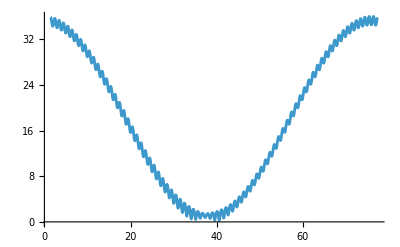

```mathematica
Plot[d[x],Prepend[itv,x]]
```

## Answer

```mathematica
DatePlus[CurrentDate["Hour"],time-Quantity[yearOffset,"JulianYears"]];
DateString[%]
```

Fri 9 Dec 2061 3 am

```mathematica
time
```

37.8732 a

```mathematica
mtime=QuantityMagnitude[time];(* julian years *)
rotTE=QuantityMagnitude[earth["RotationPeriod"],"Hours"];(* hours *)
rotdxE=QuantityMagnitude[time,"Hours"]/rotTE; (* rots *)
rotdxE=SetPrecision[(rotdxE-Floor[rotdxE])*360,8];
angcoords=ToSphericalCoordinates[halleyOrbit[mtime]-earthOrbit[mtime]][[2;;3]]*180/Pi
```

{117.066,92.6488}

```mathematica
lat=90-angcoords[[1]]+QuantityMagnitude[axialtiltE];
long=Mod[angcoords[[2]]-rotdxE,360];
If[lat>90,Print[long=Mod[long+180,360]];lat-=90];
pos=GeoPosition[{lat,long}]
```

GeoPosition[{-3.62616,70.3241}]

```mathematica
GeoNearest["City",pos];
GeoListPlot[%,GeoLabels->Automatic,GeoRange->"Country"]
Show[
GeoListPlot[%%,GeoLabels->Automatic,GeoRange->"World"],
GeoGraphics[GeoPath[{"Parallel",lat}]]
]
```

GeoGraphics::entgr: Unable to find geo range implied by GeoRange->Country.

-Graphics-

-Graphics-

```mathematica
Show[
halleyPlot,
earthPlot,
Graphics3D[{
Red,Ball[earthOrbit[mtime],0.4],
Blue,Ball[halleyOrbit[mtime],0.1]
}],
PlotRange->{{-1,2},{-2,1},{-1.5,2}},
ViewPoint->{-2, 4, 0}
]
```

-Graphics3D-